# LGD: Electrocalorics for PSTO

## Load Data:

```mathematica
(*"StringFormat"->{"    ","Qx[%]","    ","Qy[%]","    ","Qx[A]","    ","Qy[A]","    ","|Q|[A]","    ","Px[C/m^2]","    ","Py[C/m^2]","       ","|P| [C/m^2]"}*)
(*Need to save as .xlsx first in LibreOffice after cutting the space delimiters with fixed width and then save as .csv, (should give option for "," delimiters, then can open as .csv*)
```

```mathematica
a1pcComp=Import["/home/john/PSTO_stuff_Byounghak/QPdata/1pcComp.csv","Data"];Dimensions[a1pcComp];
```

```mathematica
a2pcComp=Import["/home/john/PSTO_stuff_Byounghak/QPdata/2pcComp.csv","Data"];Dimensions[a2pcComp];
```

```mathematica
a1pcTens=Import["/home/john/PSTO_stuff_Byounghak/QPdata/1pcTens.csv","Data"];Dimensions[a1pcTens];
```

```mathematica
a2pcTens=Import["/home/john/PSTO_stuff_Byounghak/QPdata/1pcComp.csv","Data"];Dimensions[a2pcTens];
```

```mathematica
aUnstr=Import["/home/john/PSTO_stuff_Byounghak/QPdata/unstrained.csv","Data"];Dimensions[aUnstr];
```

```mathematica
EgUnstr=Import["/home/john/PSTO_stuff_Byounghak/QPdata/frozen_G1G2_data_3D_unstrained.csv","Data"];Dimensions[EgUnstr];
```

```mathematica
Eg1pcComp=Import["/home/john/PSTO_stuff_Byounghak/QPdata/frozen_G1G2_data_3D_squeeze1.csv","Data"];Dimensions[Eg1pcComp];
```

```mathematica
Eg2pcComp=Import["/home/john/PSTO_stuff_Byounghak/QPdata/frozen_G1G2_data_3D_squeeze2.csv","Data"];Dimensions[Eg2pcComp];
```

```mathematica
Eg1pcTens=Import["/home/john/PSTO_stuff_Byounghak/QPdata/frozen_G1G2_data_3D_stretch1.csv","Data"];Dimensions[Eg1pcTens];
```

```mathematica
Eg2pcTens=Import["/home/john/PSTO_stuff_Byounghak/QPdata/frozen_G1G2_data_3D_stretch2.csv","Data"];Dimensions[Eg2pcTens];
```

```mathematica
(*Manipulate[{Plot[Nest[Function[t,1/(1+t)],x,j],{x,-3,3}],Nest[Function[t,1/(1+t)],x,j]},{j,3,15,1}]*)
```

Serge’s data needs the following list... since we only want Q_(x,y) ≤ 15

```mathematica
list1=Flatten[{Table[j,{j,1,16}],
Table[j,{j,16+12,16+12+14}],
Table[j,{j,16+(2*12)+14,16+(2*12)+14+13}],
Table[j,{j,16+(3*12)+14+13,16+(3*12)+14+13+12}],
Table[j,{j,16+(4*12)+14+13+12,16+(4*12)+14+13+12+11}],
Table[j,{j,16+(5*12)+14+13+12+11,16+(5*12)+14+13+12+11+10}],
Table[j,{j,16+(6*12)+14+13+12+11+10,16+(6*12)+14+13+12+11+10+9}],
Table[j,{j,16+(7*12)+14+13+12+11+10+9,16+(7*12)+14+13+12+11+10+9+8}],
Table[j,{j,16+(8*12)+14+13+12+11+10+9+8,16+(8*12)+14+13+12+11+10+9+8+7}],
Table[j,{j,16+(9*12)+14+13+12+11+10+9+8+7,16+(9*12)+14+13+12+11+10+9+8+7+6}],
Table[j,{j,16+(10*12)+14+13+12+11+10+9+8+7+6,16+(10*12)+14+13+12+11+10+9+8+7+6+5}],
Table[j,{j,16+(11*12)+14+13+12+11+10+9+8+7+6+5,16+(11*12)+14+13+12+11+10+9+8+7+6+5+4}],
Table[j,{j,16+(12*12)+14+13+12+11+10+9+8+7+6+5+4,16+(12*12)+14+13+12+11+10+9+8+7+6+5+4+3}],
Table[j,{j,16+(13*12)+14+13+12+11+10+9+8+7+6+5+4+3,16+(13*12)+14+13+12+11+10+9+8+7+6+5+4+3+2}],
Table[j,{j,16+(14*12)+14+13+12+11+10+9+8+7+6+5+4+3+2,16+(14*12)+14+13+12+11+10+9+8+7+6+5+4+3+2+1}],
Table[j,{j,16+(15*12)+14+13+12+11+10+9+8+7+6+5+4+3+2+1,16+(15*12)+14+13+12+11+10+9+8+7+6+5+4+3+2+1}]
}];
```

```mathematica
pxUnstr =Table[aUnstr[[k,6]],{k,list1}];
pyUnstr = Table[aUnstr[[k,7]],{k,list1}];
px1pcComp=Table[a1pcComp[[k,6]],{k,list1}];
py1pcComp=Table[a1pcComp[[k,7]],{k,list1}]; 
px1pcTens=Table[a1pcTens[[k,6]],{k,list1}];
py1pcTens=Table[a1pcTens[[k,7]],{k,list1}]; 
px2pcComp=Table[a2pcComp[[k,6]],{k,list1}];
py2pcComp=Table[a2pcComp[[k,7]],{k,list1}];
px2pcTens=Table[a2pcTens[[k,6]],{k,list1}];py2pcTens=Table[a2pcTens[[k,7]],{k,list1}];
```

```mathematica
{px2pcTens[[Length[list1]]],py2pcTens[[Length[list1]]]}
```

{-0.295344,-0.295344}

To convert Rydbergs to Joules, we first need the volume of the unit cell. We can fit this using the data in the DFT data. Note that the adata and cdata are in Angstroms. -0.001 represents unitless biaxial tension (-1% of the lattice constant a.

```mathematica
adata={{-0.002,7.140671*0.529177249},{-0.001,7.213535*0.529177249},{0,7.286399*0.529177249},{0.001,7.359263*0.529177249},{0.002,7.432127*0.529177249}};adatafit=Fit[adata,{1,ϵ},ϵ]
```

3.8558+38.558 ϵ

```mathematica
cdata={{-0.002,7.140671 5.396907*0.529177249},{-0.001,7.213535 5.301357*0.529177249},{0,7.286399 5.209367*0.529177249},{0.001,7.359263 5.12151*0.529177249},{0.002,7.432127 5.03693*0.529177249}};cdatafit=Fit[cdata,{1,ϵ},ϵ]
```

20.0942-145.833 ϵ

```mathematica
alattice[ϵ_]:=3.8558+38.558 ϵ;clattice[ϵ_]:=20.087-145.83ϵ; Vunit[ϵ_]:=alattice[ϵ]^2 clattice[ϵ] (10^-30);(* ϵ^2 should be in clattice term but not in alattice term *)
```

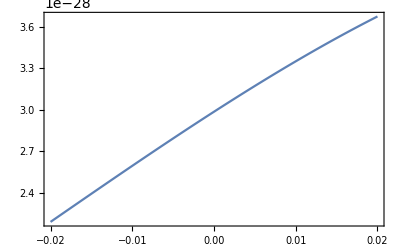
{-Graphics-,((20.087-145.83 ϵ) (3.8558+38.558 ϵ)^2)/1000000000000000000000000000000}

```mathematica
{Plot[Vunit[x],{x,-0.02,0.02},Frame->True,ImageSize->400],Vunit[ϵ]}
```

```mathematica
Tens1pcContdat1=Table[{-px1pcTens[[k]],py1pcTens[[k]],Eg1pcTens[[k,1]]/(2 Vunit[-0.01])(2.17896013*10^-18)},{k,1,136}];
Tens1pcContdat2=Table[{py1pcTens[[k]],-px1pcTens[[k]],Eg1pcTens[[k,1]]/(2 Vunit[-0.01])(2.17896013*10^-18)},{k,1,136}];
Tens2pcContdat1=Table[{-px2pcTens[[k]],-py2pcTens[[k]],Eg2pcTens[[k,1]]/(2Vunit[-0.02])(2.17896013*10^-18)},{k,1,136}];
Tens2pcContdat2=Table[{-py2pcTens[[k]],-px2pcTens[[k]],Eg2pcTens[[k,1]]/(2 Vunit[-0.02])(2.17896013*10^-18)},{k,1,136}];
Comp1pcContdat1=Table[{-px1pcComp[[k]],-py1pcComp[[k]],Eg1pcComp[[k,1]]/(2 Vunit[0.01])(2.17896013*10^-18)},{k,1,136}];
Comp1pcContdat2=Table[{-py1pcComp[[k]],-px1pcComp[[k]],Eg1pcComp[[k,1]]/(2 Vunit[0.01])(2.17896013*10^-18)},{k,1,136}];
Comp2pcContdat1=Table[{-px2pcComp[[k]],py2pcComp[[k]],Eg2pcComp[[k,1]]/(2 Vunit[0.02])(2.17896013*10^-18)},{k,1,136}];
Comp2pcContdat2=Table[{py2pcComp[[k]],-px2pcComp[[k]],Eg2pcComp[[k,1]]/(2 Vunit[0.02])(2.17896013*10^-18)},{k,1,136}];
UnstrContdat1=Table[{pxUnstr[[k]],pyUnstr[[k]],EgUnstr[[k,1]]/(2 Vunit[0])(2.17896013*10^-18)},{k,1,136}];
UnstrContdat2=Table[{pyUnstr[[k]],pxUnstr[[k]],EgUnstr[[k,1]]/(2 Vunit[0])(2.17896013*10^-18)},{k,1,136}];
```

```mathematica
ListPlot3D[{Tens2pcContdat1,Tens2pcContdat2},ImageSize->800,AxesLabel->{"P_x [C/m^2]","P_y [C/m^2]","G [J/m^3]"},BaseStyle->{FontWeight->"Bold",FontSize->18}];(*need to concatenate them somehow.. *)
```

```mathematica
Tens1pcdata= Catenate[{Tens1pcContdat1,Tens1pcContdat2}];(*Join[] does not work; use Catenate[] instead*)
Tens2pcdata = Catenate[{Tens2pcContdat1,Tens2pcContdat2}];
Comp1pcdata = Catenate[{Comp1pcContdat1,Comp1pcContdat2}];
Comp2pcdata = Catenate[{Comp2pcContdat1,Comp2pcContdat2}]; (*for some reason, some of these need px->py but some need px->-py*)
Unstrdata = Catenate[{UnstrContdat1,UnstrContdat2}];
```

```mathematica
Unstrdata[[1]][[3]]
```

-5.12891×10^12

```mathematica
ListPlot3D[Tens2pcdata,ImageSize->800,AxesLabel->{"P_x [C/m^2]","P_y [C/m^2]"},BaseStyle->{FontWeight->"Bold",FontSize->14},ColorFunction->ColorData["TemperatureMap"]]; (*shows that our catenation is working*)
```

Finally, in order to fit these data to one functional, we need to reconstruct the above tables to include ϵ as an additional independent variable. This should avoid the renormalization that happens at different strains.

```mathematica
FitDatTens1pc1=Table[{-px1pcTens[[k]],py1pcTens[[k]],-0.01,Eg1pcTens[[k,1]]/(2Vunit[0])(2.17896013*10^-18)-Unstrdata[[1]][[3]]},{k,1,136}];
```

```mathematica
FitDatTens1pc2=Table[{py1pcTens[[k]],-px1pcTens[[k]],-0.01,Eg1pcTens[[k,1]]/(2 Vunit[0])(2.17896013*10^-18)-Unstrdata[[1]][[3]]},{k,1,136}];FitDatTens1pc=Catenate[{FitDatTens1pc1,FitDatTens1pc2}];
```

```mathematica
FitDatTens2pc1=Table[{-px2pcTens[[k]],-py2pcTens[[k]],-0.02,Eg2pcTens[[k,1]]/(2Vunit[0])(2.17896013*10^-18)-Unstrdata[[1]][[3]]},{k,1,136}];
```

```mathematica
FitDatTens2pc2=Table[{-py2pcTens[[k]],-px2pcTens[[k]],-0.02,Eg2pcTens[[k,1]]/(2 Vunit[0])(2.17896013*10^-18)-Unstrdata[[1]][[3]]},{k,1,136}];FitDatTens2pc=Catenate[{FitDatTens2pc1,FitDatTens2pc2}];
```

```mathematica
FitDatComp1pc1 =Table[{-px1pcComp[[k]],-py1pcComp[[k]],0.01,Eg1pcComp[[k,1]]/(2Vunit[0])(2.17896013*10^-18)-Unstrdata[[1]][[3]]},{k,1,136}];
```

```mathematica
FitDatComp1pc2 =Table[{-py1pcComp[[k]],-px1pcComp[[k]],0.01,Eg1pcComp[[k,1]]/(2Vunit[0])(2.17896013*10^-18)-Unstrdata[[1]][[3]]},{k,1,136}];FitDatComp1pc=Catenate[{FitDatComp1pc1,FitDatComp1pc2}];
```

```mathematica
FitDatComp2pc1=Table[{-px2pcComp[[k]],py2pcComp[[k]],0.02,Eg2pcComp[[k,1]]/(2Vunit[0])(2.17896013*10^-18)-Unstrdata[[1]][[3]]},{k,1,136}];
```

```mathematica
FitDatComp2pc2=Table[{py2pcComp[[k]],-px2pcComp[[k]],0.02,Eg2pcComp[[k,1]]/(2Vunit[0])(2.17896013*10^-18)-Unstrdata[[1]][[3]]},{k,1,136}];FitDatComp2pc=Catenate[{FitDatComp2pc1,FitDatComp2pc2}];
```

```mathematica
FitDatUnstr1=Table[{pxUnstr[[k]],pyUnstr[[k]],0,EgUnstr[[k,1]]/(2Vunit[0])(2.17896013*10^-18)-Unstrdata[[1]][[3]]},{k,1,136}];
FitDatUnstr2=Table[{pyUnstr[[k]],pxUnstr[[k]],0,EgUnstr[[k,1]]/(2 Vunit[0])(2.17896013*10^-18)-Unstrdata[[1]][[3]]},{k,1,136}];
FitDatUnstr=Catenate[{FitDatUnstr1,FitDatUnstr2}];
```

```mathematica
FitData=Catenate[{FitDatTens2pc,FitDatTens1pc,FitDatUnstr,FitDatComp1pc,FitDatComp2pc}]; (* a bit of an issue fitting everything*)
```

## P-ϵ coupling fit(different functional for each):

fit with respect to 0 Energy... (or 3D fit: use ϵ in the Table... make a vector of constant 0.001...); identify the constants that don’t matter... there is also some bugs

```mathematica
fitUnstr[Px_,Py_]:=NonlinearModelFit[Unstrdata,α1(Px^2+Py^2)+α2(Px^4+Py^4)+α3 Px^2 Py^2+α4(Px^6+Py^6)+α5(Px^4 Py^2+Px^2 Py^4)+(χ1(Px^2+Py^2)+χ2 Px^2 Py^2+χ3 (Px^4+Py^4))(0)+χ4((Px^2+Py^2)+χ5 Px^2 Py^2+χ6(Px^4+Py^4))(0)^2+C0 (0)^2,{α1,α2,α3,α4,α5,χ1,χ2,χ3,χ4,χ5,χ6,C0},{Px,Py}]
```

```mathematica
fitTens1pc[Px_,Py_]:=NonlinearModelFit[Tens1pcdata,α1(Px^2+Py^2)+α2(Px^4+Py^4)+α3 Px^2 Py^2+α4(Px^6+Py^6)+α5(Px^4 Py^2+Px^2 Py^4)+(χ1(Px^2+Py^2)+χ2 Px^2 Py^2+χ3 (Px^4+Py^4))(-0.001)+(χ4(Px^2+Py^2)+χ5 Px^2 Py^2+χ6(Px^4+Py^4))(-0.001)^2+C0 (-0.001)^2,{α1,α2,α3,α4,α5,χ1,χ2,χ3,χ4,χ5,χ6,C0},{Px,Py}]
```

```mathematica
fitTens2pc[Px_,Py_]:=NonlinearModelFit[Tens2pcdata,α1(Px^2+Py^2)+α2(Px^4+Py^4)+α3 Px^2 Py^2+α4(Px^6+Py^6)+α5(Px^4 Py^2+Px^2 Py^4)+(χ1(Px^2+Py^2)+χ2 Px^2 Py^2+χ3 (Px^4+Py^4))(-0.002)+(χ4(Px^2+Py^2)+χ5 Px^2 Py^2+χ6(Px^4+Py^4))(-0.002)^2+C0 (-0.002)^2,{α1,α2,α3,α4,α5,χ1,χ2,χ3,χ4,χ5,χ6,C0},{Px,Py}]
```

```mathematica
fitComp1pc[Px_,Py_]:=NonlinearModelFit[Comp1pcdata,α1(Px^2+Py^2)+α2(Px^4+Py^4)+α3 Px^2 Py^2+α4(Px^6+Py^6)+α5(Px^4 Py^2+Px^2 Py^4)+(χ1(Px^2+Py^2)+χ2 Px^2 Py^2+χ3 (Px^4+Py^4))(0.001)+(χ4(Px^2+Py^2)+χ5 Px^2 Py^2+χ6(Px^4+Py^4))(0.001)^2+C0 (0.001)^2,{α1,α2,α3,α4,α5,χ1,χ2,χ3,χ4,χ5,χ6,C0},{Px,Py}]
```

```mathematica
fitComp2pc[Px_,Py_]:=NonlinearModelFit[Comp2pcdata,α1(Px^2+Py^2)+α2(Px^4+Py^4)+α3 Px^2 Py^2+α4(Px^6+Py^6)+α5(Px^4 Py^2+Px^2 Py^4)+(χ1(Px^2+Py^2)+χ2 Px^2 Py^2+χ3 (Px^4+Py^4))(0.002)+(χ4(Px^2+Py^2)+χ5 Px^2 Py^2+χ6(Px^4+Py^4))(0.002)^2+C0 (0.002)^2,{α1,α2,α3,α4,α5,χ1,χ2,χ3,χ4,χ5,χ6,C0},{Px,Py}]
```

```mathematica
a= "Rainbow";b= 315;q=100;plotFont={FontWeight->"Bold",FontSize->10};(*rainbow looks good but it would be nice to have a blue to white colorscheme that I saw a few weeks ago... *)
```

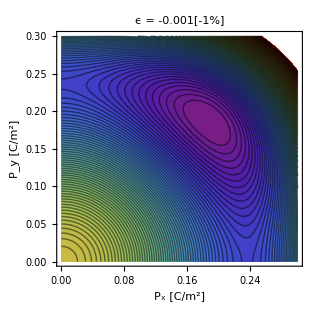
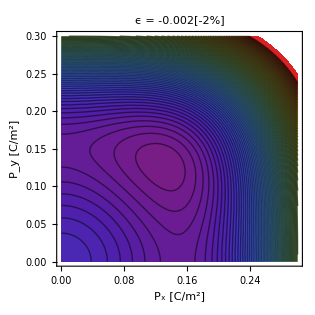
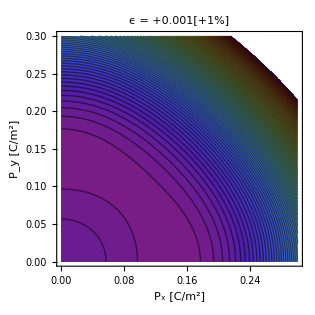
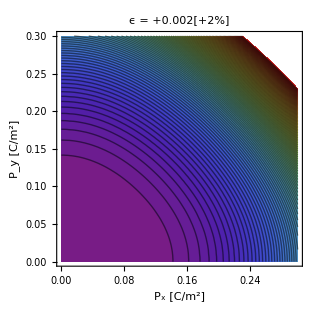
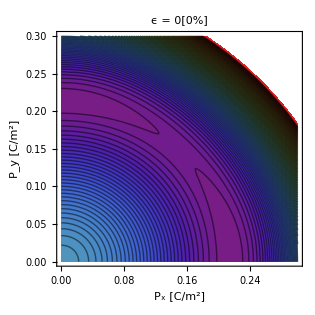

```mathematica
{{{ContourPlot[-5.195317868639679*^12+5.64520456912171*^8 Px^2 Py^2-5.421277865634533*^7 (Px^2+Py^2)+5.0249257541424495*^8 (Px^4+Py^4)+6.4763197713500395*^7 (Px^4 Py^2+Px^2 Py^4)-5.789852583600186*^8 (Px^6+Py^6)+0.001 (5.645204566790557*^11 Px^2 Py^2-5.421277868349724*^10 (Px^2+Py^2)+5.024925754907925*^11 (Px^4+Py^4))+1.*^-6 (5.645204566562084*^14 Px^2 Py^2-5.421277867731191*^13 (Px^2+Py^2)+5.024925754780281*^14 (Px^4+Py^4)),{Px,0,.3},{Py,0,.3},FrameLabel->{"P_x [C/m^2]","P_y [C/m^2]"},BaseStyle->plotFont,PlotLabel->"ϵ = -0.001[-1%]",ColorFunction->ColorData[a],ImageSize->b,Contours->q],ContourPlot[-5.263903423581602*^12+2.431114583017393*^9 Px^2 Py^2-1.5512692373511547*^8 (Px^2+Py^2)+3.5990315602491198*^9 (Px^4+Py^4)-1.1700349542295732*^10 (Px^4 Py^2+Px^2 Py^4)-1.0079326682877092*^10 (Px^6+Py^6)+0.002 (1.215557290812139*^12 Px^2 Py^2-7.756346186367783*^10 (Px^2+Py^2)+1.7995157801716272*^12 (Px^4+Py^4))+4.*^-6 (6.077786455235666*^14 Px^2 Py^2-3.878173093061345*^13 (Px^2+Py^2)+8.997578900465546*^14 (Px^4+Py^4)),{Px,0,.3},{Py,0,.3},FrameLabel->{"P_x [C/m^2]","P_y [C/m^2]"},BaseStyle->plotFont,PlotLabel->"ϵ = -0.002[-2%]",ColorFunction->ColorData[a],ImageSize->b,Contours->q]},{ContourPlot[-5.064597835750846*^12+1.860273546928744*^9 Px^2 Py^2-3.095638608461479*^7 (Px^2+Py^2)+7.797659325416497*^8 (Px^4+Py^4)+6.935556073594387*^9 (Px^4 Py^2+Px^2 Py^4)-1.3687308849516544*^9 (Px^6+Py^6)-0.001 (-1.8602735454846345*^12 Px^2 Py^2+3.095638607571566*^10 (Px^2+Py^2)-7.79765932598817*^11 (Px^4+Py^4))+1.*^-6 (1.8602735459546235*^15 Px^2 Py^2-3.0956386071191477*^13 (Px^2+Py^2)+7.797659324482998*^14 (Px^4+Py^4)),{Px,0,.3},{Py,0,.3},FrameLabel->{"P_x [C/m^2]","P_y [C/m^2]"},BaseStyle->plotFont,PlotLabel->"ϵ = +0.001[+1%]",ColorFunction->ColorData[a],ImageSize->b,Contours->q],ContourPlot[-5.002304606681014*^12+3.001418256645291*^9 Px^2 Py^2-4.698214543690165*^6 (Px^2+Py^2)+1.1492036330565152*^9 (Px^4+Py^4)+1.3069012383291193*^10 (Px^4 Py^2+Px^2 Py^4)-2.368544440173616*^9 (Px^6+Py^6)-0.002 (-1.5007091290095178*^12 Px^2 Py^2+2.34910729321518*^9 (Px^2+Py^2)-5.746018164500502*^11 (Px^4+Py^4))+4.*^-6 (7.503545640742764*^14 Px^2 Py^2-1.1745536464761624*^12 (Px^2+Py^2)+2.8730090825769506*^14 (Px^4+Py^4)),{Px,0,.3},{Py,0,.3},FrameLabel->{"P_x [C/m^2]","P_y [C/m^2]"},BaseStyle->plotFont,PlotLabel->"ϵ = +0.002[+2%]",ColorFunction->ColorData[a],ImageSize->b,Contours->q]}},ContourPlot[-5.1289098321097295*^12+3.13181210197429*^9 Px^2 Py^2-1.4220345196533558*^8 (Px^2+Py^2)+1.5826472307471724*^9 (Px^4+Py^4)+2.8109151633161163*^9 (Px^4 Py^2+Px^2 Py^4)-5.208926938792195*^8 (Px^6+Py^6),{Px,0,.3},{Py,0,.3},FrameLabel->{"P_x [C/m^2]","P_y [C/m^2]"},BaseStyle->plotFont,PlotLabel->"ϵ = 0[0%]",ColorFunction->a,ImageSize->b,Contours->q]}
```

```mathematica
Normal[fitUnstr[Px,Py]]
```

2.99608×10^15 Px^2 Py^2-2.2654×10^14 (Px^2+Py^2)+3.22286×10^15 (Px^4+Py^4)-1.2801×10^16 (Px^4 Py^2+Px^2 Py^4)-1.4342×10^16 (Px^6+Py^6)

```mathematica
NSolve[-2.2654016354817856*^14==α(0-120),α]
```

{{α→1.88783×10^12}}

```mathematica
Funstr[Px_,Py_,T_,Ex_,Ey_]:=2.996081345367319*^15 Px^2 Py^2-1.8878346962348213*^12(T-120)(Px^2+Py^2)+3.2228624639462805*^15 (Px^4+Py^4)-1.280104236184385*^16 (Px^4 Py^2+Px^2 Py^4)-1.4342018836720334*^16 (Px^6+Py^6)+Px Ex + Py Ey
```

```mathematica
Funstr[Px,Py,T,Ex,0]
```

Ex Px+2.99608×10^15 Px^2 Py^2+3.22286×10^15 (Px^4+Py^4)-1.2801×10^16 (Px^4 Py^2+Px^2 Py^4)-1.4342×10^16 (Px^6+Py^6)-1.88783×10^12 (Px^2+Py^2) (-120+T)

```mathematica
ϕ=1;equilibPSTOunstr=Table[Solve[{D[Funstr[Px,Py,T,0,0],Px]==0,D[Funstr[Px,Py,T,0,0],Py]==0,Px>0,Py>0},{Px,Py}],{T,0,300,ϕ}];Dimensions[equilibPSTOunstr]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

{301}

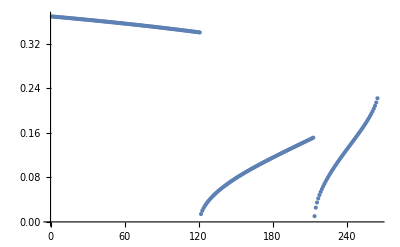

```mathematica
ListPlot[Table[Px/.Flatten[equilibPSTOunstr[[k]]],{k,1,300}]]
```

```mathematica
-5.1289098321097295*^12+3.13181210197429*^9 Px^2 Py^2-1.4220345196533558*^8 (Px^2+Py^2)+1.5826472307471724*^9 (Px^4+Py^4)+2.8109151633161163*^9 (Px^4 Py^2+Px^2 Py^4)-5.208926938792195*^8 (Px^6+Py^6)
```